```mathematica
f[x_]:=Sign[x] Abs[x]^(1/3) (* This is how to do x^(1/3) in Mathematica *)
```

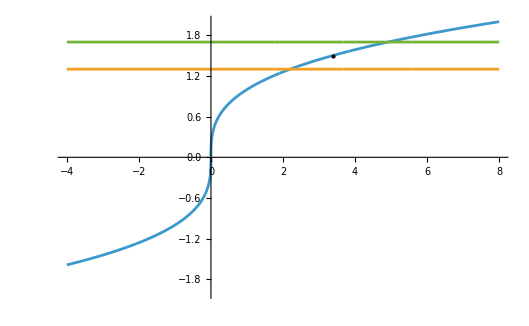

```mathematica
Show[{Plot[{f[x],1.3,1.7},{x,-4,8},PlotRange->{{-4,8},{-2.0,2.0}},PlotPoints->50000],Graphics[Point[{3.375,1.5}]]}]
```

The question is, if you want |f(x)-1.5|<0.2, what range must x be in?

It will help to know these cubes:

```mathematica
1.7^3
```

4.913

```mathematica
1.3^3
```

2.197

Knowing those cubes tells you that f(4.913)=1.7 and f(2.197)=1.3.